```mathematica
ClearAll["Global`*"]
```

```mathematica
G=6.67×10^-11;
```

```mathematica
Ek=(m×v^2)/2;
EpR=-G×(m×M)/R;
E∞=0;
```

```mathematica
r1=Solve[Ek+EpR==E∞,v]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-(0.0000115499 √M)/(√R)},{v→(0.0000115499 √M)/(√R)}}

```mathematica
v[R_,M_]=v/.r1[[2, 1]];
```

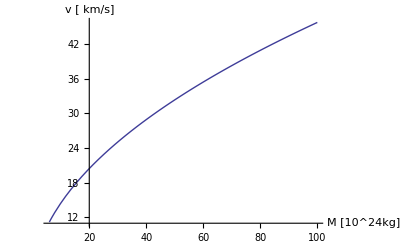

```mathematica
Plot[v[R,M×10^24]/10^3/.R->6370×10^3,{M,6,100},
AxesLabel->{"M [10^24kg]","v [ km/s]"}]
```

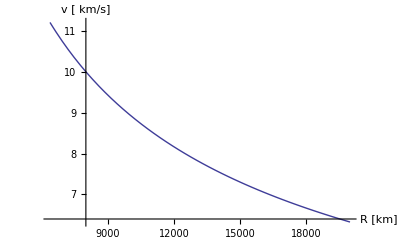

```mathematica
Plot[v[R×10^3,M]/10^3/.M->6×10^24,{R,6370,20000},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{"R [km]","v [ km/s]"}]
```